# Report Project 2

Course code: IX1500
Date: 2019-09-28

Magnus Fredriksson, magfred@kth.se
Fredrik Öberg, fobe@kth.se

Task: Break RSA Encrypted Message

## Summary

### Task

Professor Alice has sent a task to Bob, one of her students. To secure that the task really comes from her she signs the message with her private RSA key. Break the encrypted message sent to Bob.

```mathematica
nAlice=570148021012003145970598589529763010016713895412249931;
eAlice=8605;
```

```mathematica
nBob=167022448456278604446183213003807745758151706739930239;
eBob=5059;
```

```mathematica
cipher={549076974337714589255405056816906745746876377073482168,142456347182082308324976283978614881985300199557335411,353709783468365920679970049796022958453748742088527066,19263478042887342787600063478615025541128730859674239,556138488799487138099005690882531479162324546328727909,170407870245485260850117008098814771193294738253254471,129277586117065984819674612449185343180781833504915938,494619098102431837389050104623631402157378231561103085,87609997124673999454261867355123434085926380574397610,252292164093762232099109648243765435968974135008395230,374234500185817849221265037874792242624074248023214045,15252604432407291606641814269612747085204303428880441,521916249261327878342407067264626845762050945925420311,493148540210094161835172647170687913024819138535787583,11334844828170627075389984405865818554795703144674067,50888917923606415366596310575964882098718142932805625,288515903282977334639366924808488562252551530762911146,217908630560354150209207723353767699458420043574652347,232832825707285018581894380702410514587258457479379852,356233207208268263538174191567583933909172872447569250,272363441132024011404848500623376254979357697605510180,273435079770316790567752210801193474130207872150968241,540017424431459940663232027182560092553177590494279221};
```

Every number in the matrix is of basically the same size. Why?

### Result

The two public n-numbers were factorized into the two prime numbers (p, q) they were a product of.  The Φ-number of p*q where calculated through Euler’s totient function which is the basis for calculating the numbers e and p of an RSA- encryption.

The two e-numbers (one for Alice and one for Bob) were given in the assignment, but the both secret d-values where needed to be calculated. The numbers e and d are multiplicative inverses in the ring Φ((p-1)(q-1)) or you can say e*d = 1 (mod((p-1)(q-1))). With that fact stated the value of d was calculated via the method PowerMod, which makes it easy to calculate a multiplicative inverse of an element in a specific ring, or modulus value.

With all the keys in place the message sent to Bob was decrypted by first manipulating the number with Alice’s public key(eAlice) to authenticate the message. The message was then decrypted with Bob’s secret key (dBob) and the resulting number were deciphered through an algorithm which let the number go through a series of processes. Those processes included manipulating the number via a modulus function with base 256 on it with which the result was appended to a matrix, followed by dividing the number with 256. This process ended when the number had been divided down to zero and the whole message had been decrypted.

The numbers in the ascii array was converted to letters, and the message which was sent to Bob was the following:

```mathematica
"Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue the requirements for a higher grade you need to solve one more problem. The quote you should encrypt and crack is: 'The mathematician does not study pure mathematics because it is useful; he studies it because he delights in it and he delights in it because it is beautiful. By Georg Cantor, founder of set theory.'    "
```

Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue the requirements for a higher grade you need to solve one more problem. The quote you should encrypt and crack is: 'The mathematician does not study pure mathematics because it is useful; he studies it because he delights in it and he delights in it because it is beautiful. By Georg Cantor, founder of set theory.'

The final question of why the numbers in the matrix was of basically the same size is answered by looking at the encryption procedure of the RSA-encryption. When a message, M, gets encrypted it gets raised to the power of e (M^e) and when it gets decrypted it gets raised again but this time to the power of d which gives us a value of M^ed in the ring of n. Since e is inverse to d in the ring (p-1)(q-1) there is a number k such that ed = 1 + k(p-1)(q-1)

```mathematica
M^ed = M^(1 + k(p-1)*(q-1))=M*(M^(p-1)*(q-1))^k
```

Set::write: Tag Power in M^(1+k (-1+p) (-1+q)) is Protected.

Set::write: Tag Power in M^ed is Protected.

M (M^(-1+p) (-1+q))^k

With Euler’s theorem we get that

```mathematica
M^(p-1)*(q-1)≡ 1  mod(n)
```

Which makes the decrypted message D ≡ M mod n. But if M > n then the decrypted message number instead becomes M - n which is not the original message sent. M also needs to be invertible in Zn for Euler’s theorem to work, and with a number larger than n, that is not necessarily the case This states the fact that the message sent via RSA-encryption needs to be smaller than the number n, but as close to n as possible to make the message contain as much information as possible. That is the reason why the numbers in the matrix were of basically the same size.

The decrypted text also gave us a part 2 of assignment 1;
Encrypt the phrase:

"The mathematician does not study pure mathematics because it is useful; he studies it because he delights in it and he delights in it because it is beautiful. By Georg Cantor, founder of set theory."

Code was made to generate new keys, by getting random prime numbers from a range. These numbers, P, and Q, where multiplied to get N.
Another number  Φ was constructed from (P-1)(Q-1).
The message was made into a huge integer number representation by taking the ascii number representation of each number, and for each one shifting 8 more bytes into the number As soon as the number grew close to value of N, a new number was started, and the old number put in a list. The algortihm looks like this.

```mathematica
number += characters[[i]]*256^i
```

Part::pkspec1: The expression i cannot be used as a part specification.

AddTo::rvalue: number is not a variable with a value, so its value cannot be changed.

number+=256^i characters⟦i⟧

To encrypt the now properly formatted message all we need to do is to apply the encryption algorithm on each big number.
This is done in Mathematica using PowerMod[message,  receiversE, receiversN], the E value being a part of the public key and is a value that is co prime to  Φ.

To crack the message, the exact same technique as in the above task is used; two prime factors of the public key is found, and from that,  Φ and its modular inverse is found.

## Code

```mathematica
ClearAll["`*"]
```

```mathematica
(*In the assignment we were given the senders (Alice) and recipients (Bob)'s public RSA keys, and asked to decrypt a secret message*)
nBob=167022448456278604446183213003807745758151706739930239;
eBob=5059;
nAlice=570148021012003145970598589529763010016713895412249931;
eAlice=8605;
```

```mathematica
(*The RSA encryption is based on prime factorization, if sufficiently large N is chosen, the work needed to find P and Q becomes infeasible large*)
PQBOB =FactorInteger[nBob];
PQALICE =FactorInteger[nAlice];
```

```mathematica
(*These are the secret numbers that make up Bobs N value*)
"Bobs P:"
PBob = PQBOB[[1]][[1]]
```

Bobs P:

279854499601925968683787189

```mathematica
Text["Bobs Q:"]
QBob = PQBOB[[2]][[1]]
```

Bobs Q:

596818878002164343178772451

```mathematica
Text["Bobs Φ:"]
PHIBob = (PBob-1)(QBob-1)
```

Bobs Φ:

167022448456278604446183212127134368154061394877370600

```mathematica
(*To find the secret number e for bobs, we need P,Q, which make up PHI, and then we compute the modular mutliplicative inverse*)
Text["Bobs D (E's Φ's multiplicative inverse):"]
DBob = PowerMod[eBob,-1,PHIBob]
```

Bobs D (E's Φ's multiplicative inverse):

156259586586986881763942507016747769217863724442497539

```mathematica
"Bobs D (E's Φ's multiplicative inverse):"
```

Bobs D (E's Φ's multiplicative inverse):

```mathematica
(*Since Alice sent the message, we dont actually need these numbers to decrypt it, Alice's public keys will do fine, but the computation is very fast after we already did the prime factorization*)
PAlice= PQALICE[[1]][[1]];
QAlice = PQALICE[[2]][[1]];
PHIAlice = (PAlice-1)(QAlice-1);
ALICEModInv = ModularInverse[eAlice,PHIAlice];
DAlice =PowerMod[eAlice,-1,PHIAlice];
```

```mathematica
(*The message meant for Bob, that we somehow got a hold of. It has been encrypted using RSA, by alice, who also made it so that Bob could verify she's the actual sender, by encrypting twice*)
mesgAlice = {549076974337714589255405056816906745746876377073482168,142456347182082308324976283978614881985300199557335411,353709783468365920679970049796022958453748742088527066,19263478042887342787600063478615025541128730859674239,556138488799487138099005690882531479162324546328727909,170407870245485260850117008098814771193294738253254471,129277586117065984819674612449185343180781833504915938,494619098102431837389050104623631402157378231561103085,87609997124673999454261867355123434085926380574397610,252292164093762232099109648243765435968974135008395230,374234500185817849221265037874792242624074248023214045,15252604432407291606641814269612747085204303428880441,521916249261327878342407067264626845762050945925420311,493148540210094161835172647170687913024819138535787583,11334844828170627075389984405865818554795703144674067,50888917923606415366596310575964882098718142932805625,288515903282977334639366924808488562252551530762911146,217908630560354150209207723353767699458420043574652347,232832825707285018581894380702410514587258457479379852,356233207208268263538174191567583933909172872447569250,272363441132024011404848500623376254979357697605510180,273435079770316790567752210801193474130207872150968241,540017424431459940663232027182560092553177590494279221};
```

```mathematica
(*We need to decrypt twice, the first time it is to verify the sender*)
(*The sender would have encrypted with keys in order from shortest to longest, meaning that. Looking at it like LIFO stack of keys, the decryption process must use keys in reverse order*)
shortestN ;longestN;shortestDorE;longestDorE;
If[Min[nAlice, nBob] == nAlice, 
(shortestN = nAlice; longestN = nBob; shortestDorE = eAlice; longestDorE=DBob;),
(shortestN = nBob; longestN = nAlice; shortestDorE = DBob; longestDorE=eAlice;)];
```

```mathematica
(*Now the whole message can be decrypted*)
q;ascii = {};
For[i=0, i<Length[mesgAlice],i++;
(*First pass*)
curChunk = PowerMod[mesgAlice[[i]], longestDorE,longestN];
(*Second pass*)
curChunk = PowerMod[curChunk, shortestDorE, shortestN];
(*Since the bytes where packed as a huge number, we need to divide by 2^8 after each byte is read, so the message is shifted*)
q = curChunk;
While[q≠0,
AppendTo[ascii,Mod[q,256]];
q=Quotient[q,256]
];]
Text["Decrypted message:"]
TraditionalForm[FromCharacterCode[ascii]]
```

Decrypted message:

Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue the requirements for a higher grade you need to solve one more problem. The quote you should encrypt and crack is: 'The mathematician does not study pure mathematics because it is useful; he studies it because he delights in it and he delights in it because it is beautiful. By Georg Cantor, founder of set theory.'

```mathematica
(*Part 2, encrypt and crack another phrase*)
quoteToEncrypt = "The mathematician does not study pure mathematics because it is useful; he studies it because he delights in it and he delights in it because it is beautiful. By Georg Cantor, founder of set theory.";
(*There exits a receiver, let's call her alice2, bob2 will be sending her the message*)
(*Find two reasonably small prime, this is alice2's P, Q values, which make up alice2's N*)
alice2P =NextPrime[RandomInteger[{10^12,10^15}]];
alice2Q =NextPrime[RandomInteger[{10^12,10^15}]];
alice2N = alice2P*alice2Q;
alice2Phi = (alice2P-1)*(alice2Q-1)
```

271999727072053117450544373760

```mathematica
(*We also need a relative prime to alice2Phi, it can be smaller*)
alice2E = 0;
While[!CoprimeQ[alice2Phi,alice2E],alice2E = RandomInteger[{Power[10,4], Power[10,6]}] ]
alice2E
StringTake[quoteToEncrypt, {1}]
```

446563

T

```mathematica
(*Now we have everything we need for Bob2 to encrypt the message, first we need to make it into a huge number*)
bobsMessageAsNumber = {};
messageChunks = 1;
messageLen = StringLength[quoteToEncrypt];

(*We need to ensure that every part of the message is shorter than alice's public key*)
j = 0;
For[i = 1, j <  messageLen , i++,
(
k = 0;
mChunk = 0;
While[(mChunk< alice2N/256) && (j ++< messageLen ), (mChunk +=Power[256, k++]* ToCharacterCode[StringTake[quoteToEncrypt,messageLen]][[j]])];
mChunk;
AppendTo[bobsMessageAsNumber, mChunk];
)
]
bobsMessageAsNumber;
```

```mathematica
(*{55,36018043552373179236579895380,34082581649868883241514656617,35423264944617386726303757423,30766502775101707467610726501,36027351337503830274897748083,9975359118867942377610504480,32535156600329905818218554728,31383867264364039614851326068,34170441536898581936780698656,30987665488172440376348797216,32535133057028484373464837221,36027351337503830274897748084,36333554579459232126978976032,10028580078368825751852035692,34185321467808716953368813891,35939496431432603570262926692,51099145823592}*)
```

```mathematica
(*Now we encrypt each part of the message using alice's public keys*)
cBobsMessage= {};
For[i = 1, i ≤ Length[bobsMessageAsNumber], i++,
AppendTo[cBobsMessage,PowerMod[bobsMessageAsNumber[[i]],alice2E,alice2N]];
];
cBobsMessage;
```

```mathematica
(*Now that we have the message we want to crack the key that can encrypt it, this is done by prime factorizing Alice's N into P and Q*)
alice2crackedPQ =FactorInteger[alice2N];
```

```mathematica
On[Assert]
alice2crackedPorQ = alice2crackedPQ[[1]][[1]];
alice2crackedQorP = alice2crackedPQ[[2]][[1]]
alice2crackedPhi = (alice2crackedPorQ-1)(alice2crackedQorP-1);
Assert[alice2crackedPhi == alice2Phi];
alice2D = PowerMod[alice2E,-1,alice2crackedPhi];
```

619409535090161

```mathematica
(*Using the cracked keys we can decrypt the message again*)
decryptedMessage2 = {};
(*Loop through the encrypted text, decrypt and store each character*)
For[i = 1, i≤  Length[cBobsMessage], i++,
messagePart =PowerMod[cBobsMessage[[i]],alice2D,alice2N];
While[messagePart > 0, AppendTo[decryptedMessage2, FromCharacterCode[Mod[messagePart, 256]]];messagePart = Quotient[messagePart,256]; ]
]

TraditionalForm[StringJoin[decryptedMessage2]]
```

The mathematician does not study pure mathematics because it is useful; he studies it because he delights in it and he delights in it because it is beautiful. By Georg Cantor, founder of set theory.

Task: RSA breaking time estimate: Crypto analysis

## Summary

### Task

Write a method RSAcrack[cipher,n,e] that breaks an RSA encryption and returns the clear text message from a matrix of encrypted data Research the amount of time it takes to break the crypto using different sizes of n, (100-200 bits). Visualize it in a graph, and read section 2.3 to find a mathematical model. Use the model to estimate the time it would take to break a cipher where n is 1024 or 2048 buts long.

### Result

The same code as in the previous assignment was generalized to match the parameters of the RSAcrack method.

Also code to generate  P,  Q,  n,  and e was added. Setting the upper and lower bounds for p and q made it possible to get a key close to a specified size from the generation method. 
N, e, and the cipher text was sent into the RSAcrack method, and timed as the key size incremented from  ~100  to  ~200,  The discrete values of the timing makes the basis for a model to estimate the time to break much larger values.

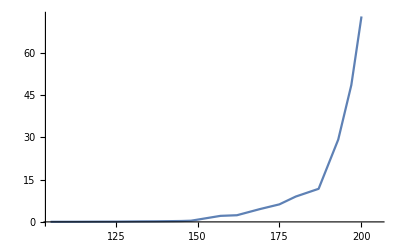
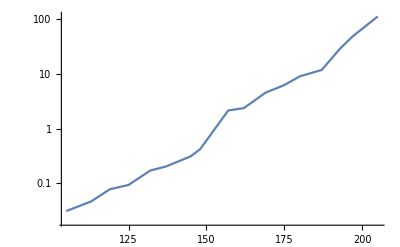
This is the results plotted into a graph.
-Graphics-
  It is quite clear that this is not a linear plot, as it does not approximate a line with linear plot axis, a Log-Log fit was also tested, but the Log-Lin plot matched a straight line best. Plotting the results onto a graph with logarithmic Y-axis gives us something more akin to a line.
  -Graphics-
  This easy test tells us that a fitting model to map this data onto a function would be an exponential one. With this knowledge we can use Mathematica to find a fitting model, but then we should first make the y axis data linear.
  The Y-axis data is run through a logarithm function, then this augmented data is, along with the regular x-axis values used in the FindFit method, where a linear model is (ax+b) is requested. 
  Mathematica can easily find fits for linear functions, and after it has succeeded, we can convert that data back into an exponential function by plugging the constants from the model into an e^(ax+b).

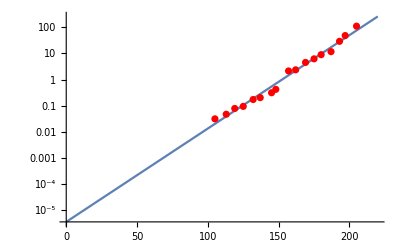

After applying this to our data, plotting the new model alongside the actual values gives us this:

The fit seems to have worked out quite well, and the model corresponds closely to reality. Now that we have verified this we can query the mathematical model for values outside the range of what we could measure earlier, due to time constraints.

For an n of length 1024, the model suggests it would take 1.51×10^31 seconds, or 4.8×10^23 years.
For an n of length 2048, the model estimates 4×10^66seconds.

## Code

```mathematica
ClearAll["`*"]
```

```mathematica
RSAcrack[cipher_,n_,e_]:=
(
Print["Cracking RSA with key length"];
Bits = Print[Round[N[Log[2, n]]]];
Print["Bits"];
crackerPQ=FactorInteger[n];
crackerPhi=(crackerPQ[[1]][[1]]-1)*(crackerPQ[[2]][[1]]-1);
crackerD=PowerMod[e,-1,crackerPhi];
zip={};
For[i=1,i≤Length[cipher],i++,messagePart=PowerMod[cipher[[i]],crackerD,n];
While[messagePart>0,AppendTo[zip,FromCharacterCode[Mod[messagePart,256]]];messagePart=Quotient[messagePart,256];]];
Return[{StringJoin[zip],Bits} ];
)
```

```mathematica
getNandEWithMaxMinRange[Min_, Max_] :=(
quoteToEncrypt = "The mathematician does not study pure mathematics because it is useful; he studies it because he delights in it and he delights in it because it is beautiful. By Georg Cantor, founder of set theory.";
(*Find two reasonably small prime, this is teh P and Q values, which make up N*)
rangeMin = Min;
rangeMax = Max;
testP =NextPrime[RandomInteger[{rangeMin,rangeMax}]];
testQ =NextPrime[RandomInteger[{rangeMin,rangeMax}]];
testN = testP*testQ;
testPhi = (testP-1)*(testQ-1);
(*We also need a relative prime to testPhi, it can be smaller*)
testE = 0;
While[!CoprimeQ[testPhi,testE],testE = RandomInteger[{Power[10,4], Power[10,6]}] ];
testMessageAsNumber = {};
messageChunks = 1;
messageLen = StringLength[quoteToEncrypt];
(*We need to ensure that every part of the message is shorter than testN key*)
j = 0;
For[i = 1, j <  messageLen , i++,
(
k = 0;
mChunk = 0;
While[(mChunk< testN/256) && (j ++< messageLen ), (mChunk +=Power[256, k++]* ToCharacterCode[StringTake[quoteToEncrypt,messageLen]][[j]])];
mChunk;
AppendTo[testMessageAsNumber, mChunk];
)
];
testMessageAsNumber;

cTestMessage = {};
For[i = 1, i ≤ Length[testMessageAsNumber], i++,AppendTo[cTestMessage,PowerMod[testMessageAsNumber[[i]],testE,testN]];];
Return [{cTestMessage, testN, testE }];
)
```

```mathematica
(*Loop, increasing key size until it reaches ~200*)
Low =50;
High = 55;
While[High < 105,
(
 testInput = getNandEWithMaxMinRange[Power[2, Low], Power[2,High]];
TimeInSeconds= Timing[RSAcrack[testInput[[1]], testInput[[2]], testInput[[3]]]][[1]];
Print[TimeInSeconds];
High += 3;
Low += 3;
)
] 
Print["Done"]
(*The above code was executed once, then the data was manually collected*)
```

Cracking RSA with key length

109

Bits

0.015625

Cracking RSA with key length

115

Bits

0.046875

Cracking RSA with key length

120

Bits

0.078125

Cracking RSA with key length

127

Bits

0.078125

Cracking RSA with key length

133

Bits

0.171875

Cracking RSA with key length

139

Bits

0.375

Cracking RSA with key length

146

Bits

0.328125

Cracking RSA with key length

149

Bits

0.5

Cracking RSA with key length

154

Bits

0.515625

Cracking RSA with key length

163

Bits

2.92188

Cracking RSA with key length

163

Bits

2.45313

Cracking RSA with key length

175

Bits

6.20313

Cracking RSA with key length

181

Bits

6.45313

Cracking RSA with key length

185

Bits

11.3125

Cracking RSA with key length

191

Bits

24.5156

Cracking RSA with key length

198

Bits

43.8281

Cracking RSA with key length

203

Bits

97.7969

Done

```mathematica
data={{105,0.03125},{113,0.046875},{119,0.078125},{125,0.09375},{132,0.171875},{137,0.203125},{145,0.3125},{148,0.421875},{157,2.14063},{162,2.35938},{169,4.53125},{175,6.21875},{180,8.98438},{187,11.7344},{193,29.1875},{197,48.5},{205,111.078}};
```

-Graphics-

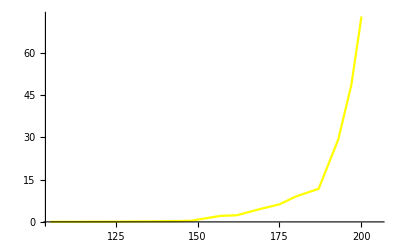

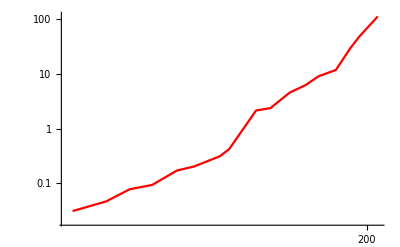

```mathematica
(*A fast way to estimate the functions character is to log it on different axis, log/lin*)
ListLogPlot[data, Joined->True]
log =ListPlot[data, Joined-> True, PlotStyle-> Yellow]
loglog =ListLogLogPlot[data, Joined->True, PlotStyle->Red]
myPlot = ListLogPlot[data, PlotStyle->Red];
```

```mathematica
(*Looking at the Logarithmic Y axis,this function seems to be an exponential function as it is a straight line more or less*)
(*Try to find a fit, since it is exponential, we need to apply logarithm to y axis for the fitfinder*)
X = data[[All, 1]];
Y = data[[All, 2]];
Clear[x];
data2=Transpose[{X,Log[Y]}];
(*Use a linear model on the modified data*)
solution=FindFit[data2,a x+b,{a,b},x]
```

{a→0.0823748,b→-12.5561}

```mathematica
aA= solution[[1]][[2]];
aB= solution[[2]][[2]];
```

```mathematica
(*Set up f(x) as an exponential function based on the fit found*)
f [x_] := Power[E, ((aA*x)+aB)];
```

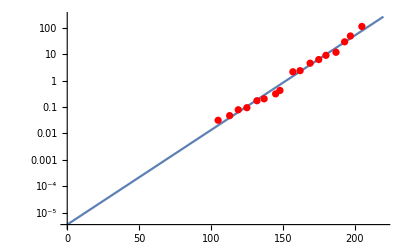

1024 len key

1.51529×10^31

2048 len key

3.95977×10^66

```mathematica
modelplot=LogPlot[f[x],{x,0,220}];
(*Compare the two plots to visually estimate the fit*)
Show[modelplot,myPlot]
"1024 len key"
f[1024]
"2048 len key"
f[2014]
```